b2 = TA 
b3 = NT 
b4 = TL

```mathematica
myColors = {RGBColor[0.0941176, 0.760784, 0.615686, 1],RGBColor[{0.6666666666666666, 0.047058823529411764, 0.7607843137254902, 1}],RGBColor[{0.9490196078431372, 0.6666666666666666, 0., 1}]} ;
```

## Input

Read in all files that have intensity data

```mathematica
myFolder = "/Volumes/BITTY/_long_timeframe_transient_mini/20190125_blind1_2_3_4_15h/Analysis/";
```

```mathematica
b2FitsFiles = FileNames[#,myFolder ]&/@{"*b2*redFitsXYCrops.dat","*b2*greenFitsXYCrops.dat","*b2*blueFitsXYCrops.dat"};
b3FitsFiles = FileNames[#,myFolder ]&/@{"*b3*redFitsXYCrops.dat","*b3*greenFitsXYCrops.dat","*b3*blueFitsXYCrops.dat"};
b4FitsFiles = FileNames[#,myFolder ]&/@{"*b4*redFitsXYCrops.dat","*b4*greenFitsXYCrops.dat","*b4*blueFitsXYCrops.dat"};
```

```mathematica
fitb2spots=  Table[ Table[ Get[(b2FitsFiles[[color,file]])], {file, 1, Length@b2FitsFiles[[color]],1}],{color, 1, Length@b2FitsFiles}];
```

```mathematica
fitb3spots=  Table[ Table[ Get[(b3FitsFiles[[color,file]])], {file, 1, Length@b3FitsFiles[[color]],1}],{color, 1, Length@b3FitsFiles}];
```

```mathematica
fitb4spots=  Table[ Table[ Get[(b4FitsFiles[[color,file]])], {file, 1, Length@b4FitsFiles[[color]],1}],{color, 1, Length@b4FitsFiles}];
```

```mathematica
myCellCountsAll = {Length@fitb2spots[[1]] , 
Length@fitb3spots[[1]] , 
Length@fitb4spots[[1]] }
```

{16,7,11}

```mathematica
redFitsb2 = fitb2spots[[1,All,1]];
redFitsb3 = fitb3spots[[1,All,1]];
redFitsb4 = fitb4spots[[1,All,1]];
```

## All cells mRNA analysis : Count, Total Intensity, and Mean Intensity

#### Visualize Counts, Means, and Totals over time

This should show the total intensity of all mRNA

```mathematica
{"mycounts","mymeans","mytotals", "mytotalsnormalized","mymeansnormalized"};
redFitsbdatab2 =Table[ 
{Length/@redFitsb2[[cell,All,All,4,2,1]],
 Mean/@redFitsb2[[cell,All,All,4,2,1]] ,
Total/@redFitsb2[[cell,All,All,4,2,1]]   }
, {cell,1,Length@redFitsb2}];
 
redFitsbdatab3 =Table[ 
{Length/@redFitsb3[[cell,All,All,4,2,1]],
 Mean/@redFitsb3[[cell,All,All,4,2,1]] ,
Total/@redFitsb3[[cell,All,All,4,2,1]]    }
, {cell,1,Length@redFitsb3}];
 
redFitsbdatab4 =Table[ 
{Length/@redFitsb4[[cell,All,All,4,2,1]],
 Mean/@redFitsb4[[cell,All,All,4,2,1]] ,
Total/@redFitsb4[[cell,All,All,4,2,1]]   }
, {cell,1,Length@redFitsb4}];
```

```mathematica
mycountsallb2 = Table[ Total[redFitsbdatab2[[All,1 (*mycounts*),time ]] ], {time, 1,Length@redFitsbdatab2[[1,1]]}] ;
 ListLinePlot[Labeled[mycountsallb2 ,"mycountsall b2 TA"]] 
mycountsallb3 = Table[ Total[redFitsbdatab3[[All,1 (*mycounts*),time ]] ], {time, 1,Length@redFitsbdatab3[[1,1]]}] ;
 ListLinePlot[Labeled[mycountsallb3 ,"mycountsall b3 NT"]] 
mycountsallb4 = Table[ Total[redFitsbdatab4[[All,1 (*mycounts*),time ]] ], {time, 1,Length@redFitsbdatab4[[1,1]]}] ;
 ListLinePlot[Labeled[mycountsallb4 ,"mycountsall b4 TL" ]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*this is BAD bc i'm totalling the means... need to pool ALL SPOTS togethr *)

mymeansallb2 = Table[ Mean[redFitsbdatab2[[All,2 (*mymeans*),time ]] ], {time, 1,Length@redFitsbdatab2[[1,1]]}] ;
ListLinePlot[Labeled[mymeansallb2 ,"mymeansall TA"]]
mymeansallb3 = Table[ Mean[redFitsbdatab3[[All,2 (*mymeans*),time ]] ], {time, 1,Length@redFitsbdatab3[[1,1]]}] ;
ListLinePlot[Labeled[mymeansallb3 ,"mymeansall NT"]]
mymeansallb4 = Table[ Mean[redFitsbdatab4[[All,2 (*mymeans*),time ]] ], {time, 1,Length@redFitsbdatab4[[1,1]]}] ;
ListLinePlot[Labeled[mymeansallb4 ,"mymeansall TL"]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
mytotsallb2 = Table[ Total[redFitsbdatab2[[All,3 (*mymeans*),time ]] ], {time, 1,Length@redFitsbdatab2[[1,1]]}] ;
mytotsallb3 = Table[ Total[redFitsbdatab3[[All,3 (*mymeans*),time ]] ], {time, 1,Length@redFitsbdatab3[[1,1]]}] ;
mytotsallb4 = Table[ Total[redFitsbdatab4[[All,3 (*mymeans*),time ]] ], {time, 1,Length@redFitsbdatab4[[1,1]]}] ;



ListLinePlot[Labeled[mytotsallb2 ,"mytotalintsall b2 TA"]]
ListLinePlot[Labeled[mytotsallb3 ,"mytotalintsall b3 NT" ]] 
ListLinePlot[Labeled[mytotsallb4 ,"mytotalintsall b4" TL]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
mytotalintstimescountsallb2  = (mytotsallb2 / mycountsallb2) ; 
ListLinePlot[{ Labeled[mytotalintstimescountsallb2 ,"totalints * countsall"], Labeled[(mycountsallb2 /105000), "counts All /105k"] }, PlotLabel-> "TA" ]
mytotalintstimescountsallb3  = (mytotsallb3 / mycountsallb3) ; 
ListLinePlot[{ Labeled[mytotalintstimescountsallb3 ,"totalints * countsall"], Labeled[(mytotsallb3 /800), "counts All /800"] } ,PlotLabel-> "NT"]
mytotalintstimescountsallb4  = (mytotsallb4 / mycountsallb4) ; 
ListLinePlot[{ Labeled[mytotalintstimescountsallb4 ,"totalints * countsall"], Labeled[(mytotsallb4 /1500), "counts All /1500"] }, PlotLabel-> "TL" ]
```

-Graphics-

-Graphics-

-Graphics-

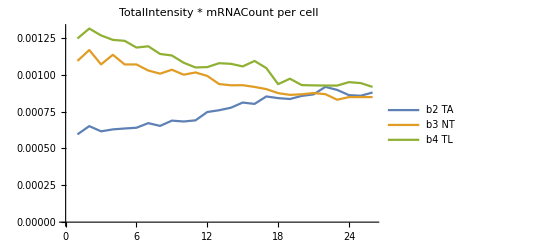

```mathematica
(*normalize to mRNA populations per cell *)
ListLinePlot[ Table[ {mytotalintstimescountsallb2,mytotalintstimescountsallb3,mytotalintstimescountsallb4} [[type]] / myCellCountsAll[[type]] , {type,1,3}],PlotLabel-> "TotalIntensity * mRNACount per cell", PlotLegends-> {"b2 TA","b3 NT","b4 TL"} ]
```

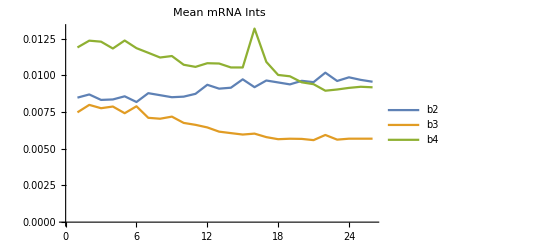

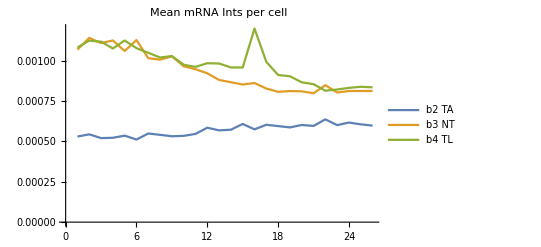

```mathematica
(*normalize to mRNA populations per cell *)
ListLinePlot[ {mymeansallb2,mymeansallb3,mymeansallb4} ,PlotLabel-> "Mean mRNA Ints", PlotLegends-> {"b2","b3","b4"} ] 
(*normalize to mRNA populations per cell *)
ListLinePlot[ Table[ {mymeansallb2,mymeansallb3,mymeansallb4} [[type]] / myCellCountsAll[[type]] , {type,1,3}],PlotLabel-> "Mean mRNA Ints per cell",  PlotLegends-> {"b2 TA","b3 NT","b4 TL"} ]
```

#### Make a histogram of mRNA intensities per cell

```mathematica
Dimensions@fitb2spots[[1,1,1]]
```

{26}

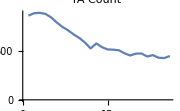

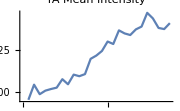

```mathematica
(*redints = Table[ redFitsb2[[cell,All,time,4,2,1]] , {cell,1,Length@redFitsb2}] ;  *)
redintsb20 = Table[ redFitsb2[[All,time,All,4,2,1]] , {time,1,Length@redFitsb2[[1]]}]  ; 
redintsb2 = Table[ Flatten[redintsb20 [[frame]] ], {frame,1,Length@redintsb20}] ; (*THIS PART might error out if the first cell isn't long enough *)
ListLinePlot[Length/@redintsb2, ImageSize->Small, PlotLabel->"TA Count"]
ListLinePlot[Mean/@redintsb2, ImageSize->Small,PlotLabel->"TA Mean Intensity"]
```

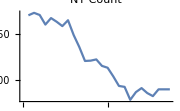

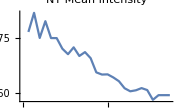

```mathematica
(*redints = Table[ redFitsb2[[cell,All,time,4,2,1]] , {cell,1,Length@redFitsb2}] ;  *)
redintsb30 = Table[ redFitsb3[[All,time,All,4,2,1]] , {time,1,Length@redFitsb3[[1]]}]  ; 
redintsb3 = Table[ Flatten[redintsb30 [[frame]] ], {frame,1,Length@redintsb30}] ; (*THIS PART might error out if the first cell isn't long enough *)
ListLinePlot[Length/@redintsb3, ImageSize->Small,PlotLabel->"NT Count"]
ListLinePlot[Mean/@redintsb3, ImageSize->Small,PlotLabel->"NT Mean Intensity"]
```

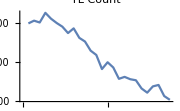

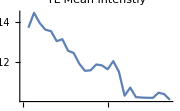

```mathematica
(*redints = Table[ redFitsb2[[cell,All,time,4,2,1]] , {cell,1,Length@redFitsb2}] ;  *)
redintsb40 = Table[ redFitsb4[[All,time,All,4,2,1]] , {time,1,Length@redFitsb4[[1]]}]  ; 
redintsb4 = Table[ Flatten[redintsb40 [[frame]] ], {frame,1,Length@redintsb40}] ; (*THIS PART might error out if the first cell isn't long enough *)
ListLinePlot[Length/@redintsb4, ImageSize->Small, PlotLabel->"TL Count"]
ListLinePlot[Mean/@redintsb4, ImageSize->Small, PlotLabel->"TL Mean Intenstiy"]
```

```mathematica
Show [ {ListLinePlot[Labeled[Length/@redintsb2/myCellCountsAll[[1]], "TA"] ] , ListLinePlot[Labeled[ Length/@redintsb3/myCellCountsAll[[2]],"NT"] ] }]
```

-Graphics-

***Normalize the intensities to 1 
Show how their intensities change during the time course

#### Normalized change of mRNA intensity plot

```mathematica
ListLinePlot[{Mean/@redintsb2 / Mean@redintsb2[[1]],Mean/@redintsb3 /Mean@redintsb3[[1]],(Mean/@redintsb4/Mean@redintsb4[[1]])}, PlotLabel->"Change of mRNA intensity " , ImageSize->500,   PlotLabels-> {"N-GFP-AGO2","GFP-AGO2", "N-GFP-LacZ"} , PlotStyle -> myColors,AxesLabel->{"Frame (30m interval)","Mean mRNA foci intensity normalized to t=0"},LabelStyle->{ FontFamily->"Arial Narrow",22,GrayLevel[.2]} ]
```

-Graphics-

```mathematica
data = {Mean/@redintsb2 / Mean@redintsb2[[1]],Mean/@redintsb3 /Mean@redintsb3[[1]],(Mean/@redintsb4/Mean@redintsb4[[1]])} ; 
myTimes = (Range[1, Length@data[[1]] ]+7)/2;
dataTime = Transpose[{myTimes,# }]&/@data ;
```

```mathematica
Length/@data
Length@myTimes
```

{26,26,26}

26

```mathematica
error = ErrorBar/@#&/@{StandardDeviation/@redintsb2 , StandardDeviation/@redintsb3 , StandardDeviation/@redintsb4 } ;
```

```mathematica
dataTimeError = Table[ Transpose[{ dataTime [[i]] , error[[i]] } ] , {i,1,3}];
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
ListLinePlot[dataTime, PlotLabel->"Change of mRNA intensity " , ImageSize->500,   PlotLabels-> {"N-GFP-AGO2","GFP-AGO2", "N-GFP-LacZ"} , PlotStyle -> myColors,LabelStyle->{ FontFamily->"Arial Narrow",18,GrayLevel[.2]}, AspectRatio->1.5  , AxesOrigin->{3.5,.5}]
```

```mathematica
myPlot0 = ErrorListPlot[dataTimeError, PlotLabel->"Change of mRNA intensity " , ImageSize->500,   PlotLabels-> {"N-GFP-AGO2","GFP-AGO2", "N-GFP-LacZ"} , PlotStyle -> myColors,LabelStyle->{ FontFamily->"Arial Narrow",24,GrayLevel[.2]}, AspectRatio->1.25  , AxesOrigin->{3.5,.5}, Joined->True] 
myPlot = Show[myPlot0, ImageSize-> 1500]
```

-Graphics-

```mathematica
Export[myFolder<>"myChangemRNAIntenstiyPlot.png",  myPlot ]
```

/Volumes/BITTY/_long_timeframe_transient_mini/20190125_blind1_2_3_4_15h/Analysis/myChangemRNAIntenstiyPlot.png

#### Count vs Intensity of mRNA plots :

```mathematica
ListLinePlot[{Length/@redintsb2, Length/@redintsb3, Length/@redintsb4}/myCellCountsAll , ImageSize->500, PlotLabel->"Mean mRNA Count per cell ", PlotLabels->  {"N-GFP-AGO2","GFP-AGO2", "N-GFP-LacZ"} ,AxesLabel->{"Frame (30m interval)"," Count of mRNA"},LabelStyle->{ FontFamily->"Arial Narrow",16,GrayLevel[.2]}] 
ListLinePlot[{Mean/@redintsb2,Mean/@redintsb3,Mean/@redintsb4}, PlotLabel->"Mean mRNA Intensity" , ImageSize->500,   PlotLabels-> {"N-GFP-AGO2","GFP-AGO2", "N-GFP-LacZ"} ,AxesLabel->{"Frame (30m interval)","Intensity of mRNA"},LabelStyle->{ FontFamily->"Arial Narrow",16,GrayLevel[.2]} ]
```

-Graphics-

-Graphics-

```mathematica
myCellCounts
```

{16,7,11}

```mathematica
ListLinePlot[({Length/@redintsb2, Length/@redintsb3, Length/@redintsb4} )*({Mean/@redintsb2,Mean/@redintsb3,Mean/@redintsb4})/myCellCounts , PlotLabels-> {"N-GFP-AGO2","GFP-AGO2", "N-GFP-LacZ"} ,AxesLabel->{"Frame (30m interval)","total intensity of mRNA per cell "},LabelStyle->{ FontFamily->"Arial Narrow",16,GrayLevel[.2]} ]
```

-Graphics-

```mathematica
redintsb20[[1]]//Dimensions
```

{16}

### Making histograms to show the distribution of mRNA signals

```mathematica
Histogram[# (* , PlotRange->Full *)]&/@redintsb2
Histogram[#, PlotRange->All ]&/@redintsb20[[1]]
```

Linear-axis histogram

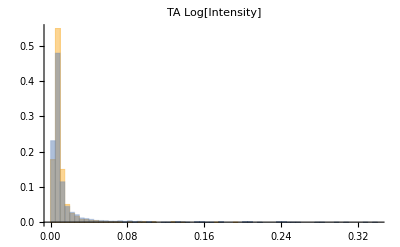

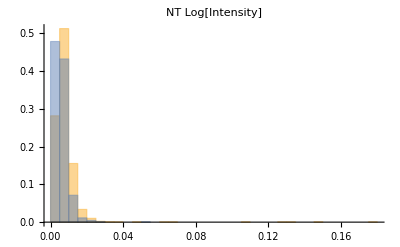

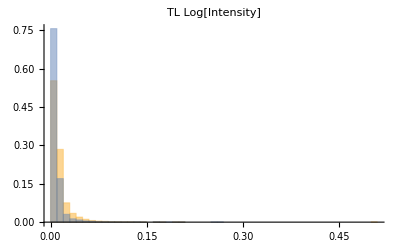

```mathematica
Histogram[{Flatten@redintsb2[[1;;5]],Flatten@redintsb2[[-5;;-1]]} , 50 , "Probability", PlotRange->All, PlotLabel->"TA Log[Intensity]" ]
Histogram[{Flatten@redintsb3[[1;;5]],Flatten@redintsb3[[-5;;-1]]}  , 50 , "Probability",  PlotRange->All ,PlotLabel->"NT Log[Intensity]" ]
Histogram[{Flatten@redintsb4[[1;;5]],Flatten@redintsb4[[-5;;-1]]}  , 50 , "Probability", PlotRange->All ,PlotLabel->"TL Log[Intensity]" ]
```

Log-axis histogram

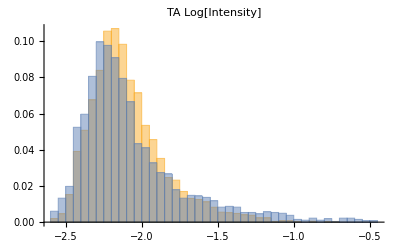

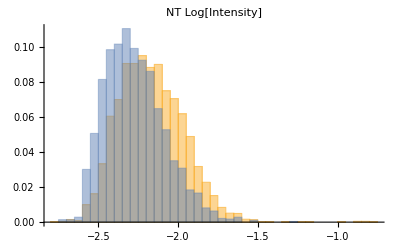

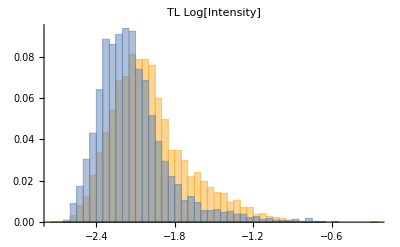

```mathematica
Histogram[{Log10/@Flatten@redintsb2[[1;;5]],Log10/@Flatten@redintsb2[[-5;;-1]]} , 50 , "Probability", PlotRange->All, PlotLabel->"TA Log[Intensity]" ]
Histogram[{Log10/@Flatten@redintsb3[[1;;5]],Log10/@Flatten@redintsb3[[-5;;-1]]}  , 50 , "Probability",  PlotRange->All ,PlotLabel->"NT Log[Intensity]" ]
Histogram[{Log10/@Flatten@redintsb4[[1;;5]],Log10/@Flatten@redintsb4[[-5;;-1]]}  , 50 , "Probability", PlotRange->All ,PlotLabel->"TL Log[Intensity]" ]
```

```mathematica
Histogram[{Log10/@Flatten@redintsb2[[1;;5]],Log10/@Flatten@redintsb2[[-5;;-1]]} , 50 , "Probability", PlotRange->All, PlotLabel->"TA Log[Intensity]" ]
Histogram[{Log10/@Flatten@redintsb3[[1;;5]],Log10/@Flatten@redintsb3[[-5;;-1]]}  , 50, "Probability" ,  PlotRange->All ,PlotLabel->"NT Log[Intensity]" ]
Histogram[{Log10/@Flatten@redintsb4[[1;;5]],Log10/@Flatten@redintsb4[[-5;;-1]]}  , 50, "Probability" , PlotRange->All ,PlotLabel->"TL Log[Intensity]" ]
```

-Graphics-

-Graphics-

-Graphics-

Histograms of the top 10% brightest spots

Pick a threshold: 
Try using “All RNA with brightness of x stdevs above the mean “

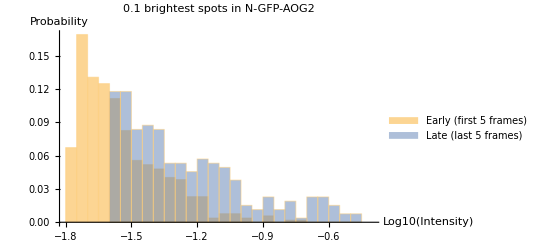

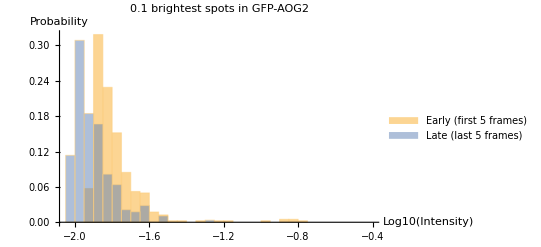

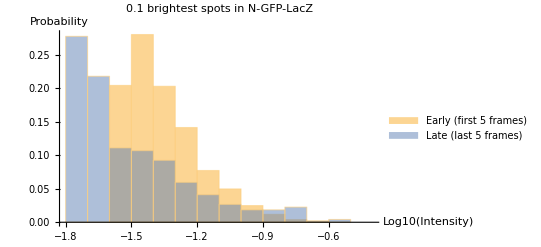

```mathematica
n = .1 ; (*The 10% brightest spots used, only*) 
tempData = Sort[#,Greater]&/@{Log10/@Flatten@redintsb2[[1;;5]],Log10/@Flatten@redintsb2[[-5;;-1]]} ;
Histogram[{tempData[[1, 1;;Ceiling@(Length@tempData[[1]]*n ) ]] , tempData[[2, 1;;Ceiling@(Length@tempData[[2]]*n ) ]] }, 20,"Probability"  , PlotLabel->( n"brightest spots in N-GFP-AOG2")  ,ChartLegends->{"Early (first 5 frames) ","Late (last 5 frames) "}, PlotLabel->( n"brightest spots in N-GFP-LacZ"), AxesLabel->{"Log10(Intensity)","Probability"}, PlotRange->{{All,-.4},{All,All}}] 

tempData = Sort[#,Greater]&/@{Log10/@Flatten@redintsb3[[1;;5]],Log10/@Flatten@redintsb3[[-5;;-1]]} ;
Histogram[{tempData[[1, 1;;Ceiling@(Length@tempData[[1]]*n ) ]] , tempData[[2, 1;;Ceiling@(Length@tempData[[2]]*n ) ]] }, 20,"Probability"  , PlotLabel->( n"brightest spots in GFP-AOG2")  ,ChartLegends->{"Early (first 5 frames) ","Late (last 5 frames) "}, PlotLabel->( n"brightest spots in N-GFP-LacZ"), AxesLabel->{"Log10(Intensity)","Probability"}, PlotRange->{{All,-.4},{All,All}}] 

tempData = Sort[#,Greater]&/@{Log10/@Flatten@redintsb4[[1;;5]],Log10/@Flatten@redintsb4[[-5;;-1]]} ;
Histogram[{tempData[[1, 1;;Ceiling@(Length@tempData[[1]]*n ) ]] , tempData[[2, 1;;Ceiling@(Length@tempData[[2]]*n ) ]] }, 20,"Probability"  ,ChartLegends->{"Early (first 5 frames) ","Late (last 5 frames) "}, PlotLabel->( n"brightest spots in N-GFP-LacZ"), AxesLabel->{"Log10(Intensity)","Probability"}, PlotRange->{{All,-.4},{All,All}}]
```

#### Remaking these histograms using the RandomChoice : (Probably don’t use)

Making a random choice of the length of the shorter of the two lists, then pulling those values into a histogram (so you have the same # of entries in each!! “normalizing” the histogram)

```mathematica
(*tempData =   RandomSample[#,tempMinLength]&/@ {Log10/@Flatten@redintsb2[[1;;5]],Log10/@Flatten@redintsb2[[-5;;-1]]} ;
Histogram[(Sort[#,Greater]&/@tempData) [[All,1;;200]] ,10]
tempData =   RandomSample[#,tempMinLength]&/@ {Log10/@Flatten@redintsb3[[1;;5]],Log10/@Flatten@redintsb3[[-5;;-1]]} ;
Histogram[(Sort[#,Greater]&/@tempData) [[All,1;;200]] ,10]
tempData =   RandomSample[#,tempMinLength]&/@ {Log10/@Flatten@redintsb4[[1;;5]],Log10/@Flatten@redintsb4[[-5;;-1]]} ;
Histogram[(Sort[#,Greater]&/@tempData) [[All,1;;200]] ,10]
```

Redo these histograms, but without the log fxn.

```mathematica
(*tempData =   RandomSample[#,tempMinLength]&/@ { Flatten@redintsb2[[1;;5]], Flatten@redintsb2[[-5;;-1]]} ;
Histogram[(Sort[#,Greater]&/@tempData) [[All,1;;150]] ,20, PlotRange->{{0,.4},{All,All}}]
tempData =   RandomSample[#,tempMinLength]&/@ { Flatten@redintsb3[[1;;5]], Flatten@redintsb3[[-5;;-1]]} ;
Histogram[(Sort[#,Greater]&/@tempData) [[All,1;;150]] ,20, PlotRange->{{0,.4},{All,All}}]
tempData =   RandomSample[#,tempMinLength]&/@ { Flatten@redintsb4[[1;;5]], Flatten@redintsb4[[-5;;-1]]} ;
Histogram[(Sort[#,Greater]&/@tempData) [[All,1;;150]] ,20, PlotRange->{{0,.4},{All,All}} ]
```

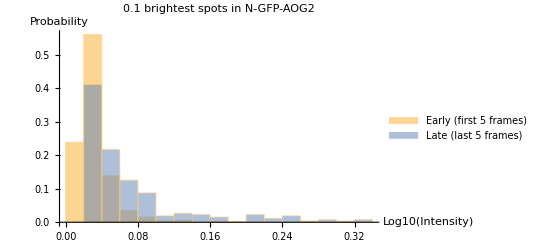

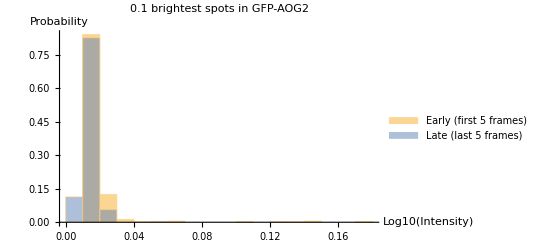

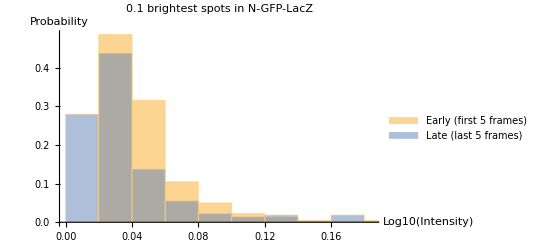

```mathematica
n = .1 ; (*The 10% brightest spots used, only*) 
tempData = Sort[#,Greater]&/@{Flatten@redintsb2[[1;;5]],Flatten@redintsb2[[-5;;-1]]} ;
Histogram[{tempData[[1, 1;;Ceiling@(Length@tempData[[1]]*n ) ]] , tempData[[2, 1;;Ceiling@(Length@tempData[[2]]*n ) ]] }, 20,"Probability"  , PlotLabel->( n"brightest spots in N-GFP-AOG2")  ,ChartLegends->{"Early (first 5 frames) ","Late (last 5 frames) "}, PlotLabel->( n"brightest spots in N-GFP-LacZ"), AxesLabel->{"Log10(Intensity)","Probability"}]

tempData = Sort[#,Greater]&/@{Flatten@redintsb3[[1;;5]],Flatten@redintsb3[[-5;;-1]]} ;
Histogram[{tempData[[1, 1;;Ceiling@(Length@tempData[[1]]*n ) ]] , tempData[[2, 1;;Ceiling@(Length@tempData[[2]]*n ) ]] }, 20,"Probability"  , PlotLabel->( n"brightest spots in GFP-AOG2")  ,ChartLegends->{"Early (first 5 frames) ","Late (last 5 frames) "}, PlotLabel->( n"brightest spots in N-GFP-LacZ"), AxesLabel->{"Log10(Intensity)","Probability"}]

tempData = Sort[#,Greater]&/@{Flatten@redintsb4[[1;;5]],Flatten@redintsb4[[-5;;-1]]} ;
Histogram[{tempData[[1, 1;;Ceiling@(Length@tempData[[1]]*n ) ]] , tempData[[2, 1;;Ceiling@(Length@tempData[[2]]*n ) ]] }, 20,"Probability"  ,ChartLegends->{"Early (first 5 frames) ","Late (last 5 frames) "}, PlotLabel->( n"brightest spots in N-GFP-LacZ"), AxesLabel->{"Log10(Intensity)","Probability"}]
```